# Steepest Descent

The best possible convergence rate for Steepest Descent is slow!

The standard theorem about Steepest Descent shows that the convergence of steepest descent on a convex quadratic function with an exact line search is slow.  Most real-world functions are not quadratic.  Most real world functions have non-convex regions. An optimal line search is impossible.

This list of unreasonably optimistic assumptions means you can write down the iteration down.

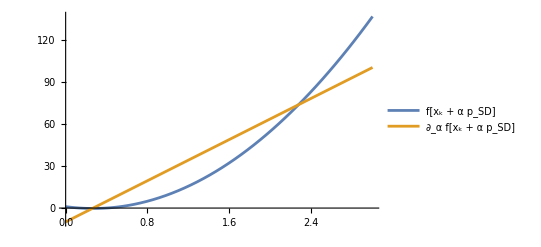

```mathematica
n=4;
A=RandomReal[{-1,1},{n,n}];A=A.Aᵀ;
g=RandomReal[{-1,1},n];
xMin=LinearSolve[A,-g];
f[x_]:=0.5 x.A.x+g.x
dxf[x_]:=A.x+g
h[x_,α_]:=f[x-α df[x]]
dαh[x_,α_]:=-df[x-α df[x]].df[x]
xk=RandomReal[{-1,1},n];
Plot[{h[xk,α],dαh[xk,α]},{α,0, 3},
PlotLegends->{"f[x_k + α p_SD]","∂_α f[x_k + α p_SD]"}]
```

Expanding
	f[x_k + α p_SD]=0.5 (x+α p_SD).A.(x+α p_SD)+g.(x+α p_SD)
gives 
	f[x_k + α p_SD]=0.5 α^2 p_SD.A.p_SD+α (g.p_SD+x.A.p_SD) + const
So 
	d/dα(f[x_k + α p_SD])=α p_SD.A.p_SD+(A.x+g).p_SD=α p_SD.A.p_SD-||p_SD(||)^2
So the ideal line search step is 
	α_k=(p_SD.p_SD)/(p_SD.A.p_SD)>0

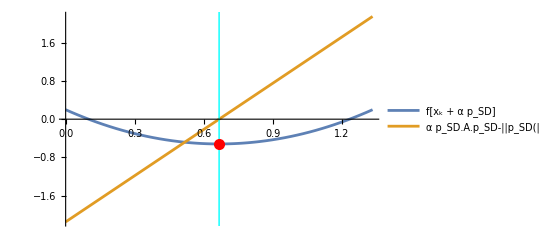

```mathematica
n=4;
A=RandomReal[{-1,1},{n,n}];A=A.Aᵀ;
g=RandomReal[{-1,1},n];
f[x_]:=0.5 x.A.x+g.x
xk=RandomReal[{-1,1},n];
pSD=-(A.xk+g);
αk=(pSD.pSD)/(pSD.A.pSD);
xNew=xk+αk pSD;
fNew=f[xNew];
Plot[{f[xk+α pSD],α pSD.A.pSD-pSD.pSD},{α,0, 2 αk},
PlotLegends->{"f[x_k + α p_SD]","α p_SD.A.p_SD-||p_SD(||)^2]"},
Epilog->{
{Cyan,Line[{{αk,-10^2},{αk,10^2}}]},
{Red,PointSize[0.02],Point[{αk,fNew}]}
}]
```

The new point is 
	x_(k+1)=x_k+α_k p_SD=x_k-(pSD.pSD)/(pSD.A.pSD)(A.x_k+g)
where p_SD=-(A.x_k+g) which we can tidy up and plug into 
	f=0.5 x.A.x+g.x
and tidy up again to get a very explicit expression for f(x_(k+1)).  It is traditional to quantify convergence in the weighted norm
	||z(||)_A:=√(z.A.z)
If you go and plug everything and tidy you get
	|| x_(k+1)-x_Min(||)_A^2=(1-(df_k.df_k)/((df_k.A.df_k)(df_k.A^-1.df_k)))|| x_k-x_Min(||)_A^2
The expression inside the parenthesis is always less than 1.  The problem is that it is only a tiny little bit less than one.  Fortunately there is a much more easily interpreted approximate bound
	|| x_(k+1)-x_Min(||)_A^2≤((λ_n-λ_1)/(λ_n+λ_1))^2|| x_k-x_Min(||)_A^2
This bound is observed in real life. Even under the best possible circumstances Steepest Descent is very slow for badly conditioned problems.  The condition number of an SPD matrix is κ=λ_n/λ_1.  A matrix is badly conditioned if κ is big.  The condition number is important because multiplying by a matrix A or solving the linear system A.x=b always reduces the accuracy by log_10(κ) decimal digits. Linear solvers usually start warning somewhere near κ≈10^7.  In terms of the condition number the steepest descent convergence constant
	(λ_n-λ_1)/(λ_n+λ_1)=(λ_n/λ_1-1)/(λ_n/λ_1+1)=(κ-1)/(κ+1)
For κ=10^7 this is 0.9999998.  This is very slow convergence.  To reduce the original error by half you need to take a lot of steps. 
	0.9999998^τ=0.5
or τ=ln(0.5)/ln(0.9999998)≈3.4657×10^6

```mathematica
Log[0.5]/Log[0.9999998]
```

3.46574×10^6

```mathematica
2^24
```

16777216

```mathematica
Data1=Table[{k,0.9999998^k},{k,0, 10^2}];
Data2=Table[k=Floor[2^p];{k,0.9999998^k},{p,0, 24,0.5}];
TabView[{
"Start"->ListPlot[Data1,GridLines->Automatic],
"BigPic"->ListLogPlot[{Data2,Data1},PlotRange->All,GridLines->Automatic]
}]
```

12

Just a reminder.  This is under the best possible circumstances.

Under the best possible circumstances Steepest Descent is slow for even a remotely badly conditioned problems.

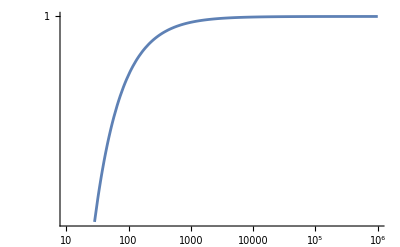

```mathematica
LogLogPlot[ (k-1)/(k+1),{k, 10, 10^6}]
```

All reasonably fast algorithms incorporate some courvature information.